```mathematica
Clear[DepthChart]
DepthChart[depth_,style_]:=BarChart[#[[;;,2]],ChartLabels->#[[;;,1]],style]&@With[{depths=#},Sort[({#[[1]],Length@#/Length@depths}&/@Gather[#]),#1[[1]]<#2[[1]]&]]&@depth
```

```mathematica
svdepths = {{8,0},{27,7},{26,2},{23,3},{20,5},{7,1},{17,2},{6,0},{18,6},{31,0},{20,5},{19,1},{13,4},{34,7},{13,3},{7,0},{24,4},{13,2},{23,3},{9,3},{24,6},{10,0},{6,0},{18,4},{16,4},{15,3},{12,3},{22,3},{9,2},{7,1},{30,4},{14,4},{11,3},{6,0},{20,3},{17,1},{10,2},{23,0},{21,0},{12,0},{8,0},{32,2},{15,2},{16,0},{10,2},{21,6},{13,2},{4,1},{5,0},{13,1},{28,1},{23,2},{20,4},{27,2},{35,2},{21,2},{11,0},{11,3},{14,0},{29,3},{6,0},{20,3},{17,1},{17,3},{9,0},{26,2},{12,0},{27,5},{34,4},{20,2},{7,0},{19,2},{26,0},{3,0},{27,3},{15,1},{11,2},{26,3},{21,1},{10,0},{25,4},{15,4},{19,3},{22,1},{8,0},{25,2},{9,1},{20,0},{31,0},{18,2},{16,0},{11,3},{11,0},{15,2},{33,3},{22,1},{16,3},{10,0},{15,3},{32,1},{25,2},{14,3},{22,2},{7,0},{21,7},{10,0},{6,2},{10,0},{10,2},{10,0},{23,2},{6,1},{25,3},{5,0},{17,4},{20,1},{12,0},{17,2},{19,1},{17,2},{10,0},{11,2},{27,4},{9,1},{24,2},{15,1},{10,3},{9,2},{26,0},{33,5},{12,3},{26,2},{21,3},{21,3},{37,2},{15,0},{14,0},{27,4},{15,2},{11,1},{8,2},{24,6},{15,2},{3,0},{29,6},{3,0},{12,2},{3,0},{21,0},{31,2},{3,0},{9,0},{15,0},{15,0},{8,0},{10,1},{20,0},{8,4},{15,0},{6,0},{12,1},{13,0},{17,3},{13,0},{32,3},{30,3},{25,4},{25,2},{17,2},{4,0},{34,1},{11,0},{17,1},{9,2},{21,6},{12,1},{12,0},{19,4},{12,2},{17,2},{7,0},{8,0},{27,0},{21,1},{19,2},{28,6},{14,4},{11,2},{21,2},{12,2},{27,6},{11,1},{14,1},{10,1},{18,2},{30,2},{23,2},{9,2},{12,2},{23,4},{23,5},{10,1},{14,1},{21,3},{10,1},{8,0},{16,1},{27,3},{24,0},{22,3},{28,1},{12,3},{34,0},{31,0},{24,1},{4,0},{2,0},{2,0},{19,2},{26,2},{15,4},{7,0},{6,2},{9,2},{10,1},{28,4},{10,0},{12,0},{12,4},{19,4},{26,1},{15,1},{11,0},{7,1},{12,3},{6,0},{9,2},{17,4},{16,3},{22,1},{20,2},{5,0},{5,0},{15,2},{27,3},{8,0},{21,4},{11,1},{6,0},{20,2},{11,3},{15,0},{23,2},{18,2},{26,4},{12,1},{16,1},{30,1},{18,2},{6,1},{9,0},{26,1},{19,3},{7,0},{12,2},{21,1},{18,1},{24,4},{25,4},{15,0},{20,2},{20,5},{9,0},{26,4},{29,0},{21,2},{12,0},{7,0},{32,4},{17,0},{21,2},{32,5},{8,0},{34,2},{23,6},{21,2},{26,0},{7,2},{19,2},{10,3},{11,1},{18,4},{11,2},{14,0},{24,3},{4,1},{5,2},{17,0},{12,0},{17,1},{21,0},{8,0},{25,2},{23,2},{3,0},{21,2},{28,3},{6,3},{13,2},{15,2},{24,2},{7,0},{21,1},{10,4},{14,1},{7,2},{8,0},{33,2},{6,1},{11,1},{22,4},{17,1},{20,0},{16,0},{11,3},{17,1},{19,0},{8,3},{20,3},{18,3},{20,0},{19,3},{24,6},{11,4},{10,2},{9,3},{13,1},{13,5},{25,1},{21,4},{26,4},{16,0},{27,7},{11,0},{8,0},{17,2},{12,0},{9,0},{12,0},{9,3},{20,4},{14,1},{23,3},{12,0},{7,1},{12,0},{13,0},{16,3},{17,3},{13,0},{27,5},{23,3},{5,0},{24,0},{16,2},{8,0},{6,0},{22,2},{11,0},{11,2},{25,0},{15,3},{17,1},{21,0},{24,3},{29,1},{17,0},{18,3},{14,2},{4,0},{11,1},{29,3},{12,2},{12,0},{17,0},{13,1},{4,0},{17,2},{25,0},{17,2},{21,2},{11,2},{20,2},{19,2},{11,1},{10,2},{24,4},{22,6},{5,0},{18,2},{8,3},{11,2},{29,7},{28,3},{6,0},{4,0},{16,4},{11,2},{8,0},{18,1},{16,0},{21,2},{20,4},{15,0},{22,0},{18,0},{16,2},{22,2},{21,2},{5,2},{13,1},{19,3},{13,0},{10,1},{20,0},{13,2},{11,6},{14,0},{15,2},{11,2},{25,0},{26,4},{12,2},{11,0},{23,1},{23,0},{29,3},{18,3},{13,4},{13,0},{30,2},{10,0},{26,2},{19,1},{11,2},{12,3},{22,5},{12,3},{10,1},{6,2},{27,4},{20,0},{24,4},{7,1},{7,1},{7,1},{24,2},{14,1},{17,3},{29,12},{10,0},{23,1},{16,0},{11,0},{7,1},{13,0},{22,3},{5,2},{23,2},{20,4},{11,4},{17,0},{23,0},{19,5},{16,9},{13,0},{10,0},{21,2},{16,2},{10,1},{11,0},{15,2},{22,5},{22,4},{7,0},{18,5},{28,2},{26,2},{25,5},{18,0},{24,2},{22,6},{15,2},{13,1},{31,6},{7,0},{9,0},{13,0},{15,0},{24,5},{26,4},{17,0},{7,2},{27,1},{6,0},{5,0},{31,6},{12,1},{12,0},{9,0},{10,0},{25,1},{13,2},{16,2},{10,0},{20,4},{11,1},{14,3},{10,2},{14,2},{12,0},{17,4},{9,1},{21,0},{8,0},{17,2},{12,0},{12,0},{30,1},{28,2},{16,0},{28,3},{9,2},{17,4},{11,3},{20,4},{19,0},{18,2},{14,0},{33,4},{5,0},{2,0},{20,1},{8,1},{6,1},{8,0},{22,3},{33,8},{24,1},{27,2},{34,2},{9,0},{25,2},{12,2},{10,0},{23,1},{9,0},{15,2},{26,2},{9,1},{9,0},{15,0},{18,0},{11,0},{9,2},{11,0},{29,7},{17,0},{20,1},{15,2},{29,3},{29,3},{7,0},{31,0},{15,2},{25,2},{21,1},{8,2},{14,0},{10,3},{18,3},{14,2},{24,2},{19,3},{26,2},{23,6},{14,4},{20,4},{6,0},{20,0},{22,3},{1,0},{10,0},{6,1},{10,0},{21,4},{27,2},{30,2},{10,0},{9,2},{9,4},{10,1},{26,3},{18,1},{34,2},{25,1},{15,0},{33,3},{6,0},{22,7},{7,0},{19,0},{15,1},{35,0},{14,0},{13,2},{18,0},{30,6},{3,0},{16,2},{17,1},{13,1},{12,4},{7,1},{14,0},{6,0},{8,0},{18,0},{12,1},{24,2},{13,3},{5,0},{31,3},{20,5},{16,2},{30,8},{22,2},{14,2},{17,0},{16,1},{30,0},{35,2},{20,1},{6,1},{12,4},{14,5},{13,1},{6,0},{6,0},{10,2},{9,2},{22,1},{13,2},{4,1},{20,7},{25,5},{15,2},{20,3},{16,3},{21,2},{25,3},{18,2},{18,3},{17,2},{24,2},{13,0},{2,0},{22,6},{17,4},{19,0},{7,1},{14,4},{25,6},{25,2},{16,2},{17,3},{5,0},{8,0},{17,3},{29,3},{20,7},{30,3},{25,1},{18,0},{28,2},{28,2},{31,4},{16,1},{17,3},{6,2},{27,7},{8,0},{30,4},{8,3},{10,2},{12,0},{14,3},{16,2},{23,0},{17,3},{14,1},{30,6},{17,2},{23,1},{8,0},{20,3},{22,4},{29,2},{17,0},{12,4},{16,0},{30,1},{24,0},{4,0},{16,3},{21,1},{12,1},{13,0},{34,8},{22,0},{19,4},{17,2},{20,2},{17,6},{10,2},{21,1},{24,4},{34,4},{21,2},{19,5},{6,0},{9,0},{16,0},{10,2},{20,5},{32,0},{24,3},{15,1},{10,0},{22,0},{8,3},{8,0},{15,0},{6,0},{29,2},{8,2},{12,2},{18,3},{18,2},{18,1},{20,4},{22,6},{9,0},{12,2},{22,3},{6,0},{29,3},{7,2},{15,2},{28,5},{19,2},{24,5},{15,2},{10,0},{9,1},{10,0},{17,4},{24,3},{36,4},{12,4},{28,4},{27,4},{13,4},{19,4},{31,2},{19,2},{15,2},{21,4},{28,6},{6,0},{16,5},{20,5},{16,2},{22,2},{18,6},{17,3},{10,3},{23,1},{11,2},{8,0},{13,3},{27,2},{16,4},{13,7},{4,1},{20,5},{13,4},{25,6},{26,8},{5,1},{14,0},{18,4},{23,6},{11,1},{27,2},{10,4},{7,0},{21,6},{13,2},{13,2},{12,0},{13,3},{11,1},{10,0},{26,6},{23,5},{30,6},{22,2},{23,3},{23,3},{13,2},{7,2},{23,5},{24,5},{16,1},{10,2},{5,0},{8,2},{7,2},{13,3},{9,0},{24,5},{13,0},{7,3},{17,4},{12,3},{21,4},{23,5},{8,2},{15,0},{16,2},{8,1},{28,3},{13,4},{12,2},{11,2},{16,1},{11,2},{10,2},{14,1},{29,5},{7,2},{16,3},{28,2},{24,5},{22,1},{27,2},{5,0},{30,2},{19,4},{13,2},{34,3},{26,6},{29,3},{13,3},{16,2},{13,1},{6,0},{23,4},{23,3},{16,4},{26,5},{8,2},{11,3},{24,8},{30,5},{25,3},{5,1},{17,3},{33,1},{10,0},{18,2},{24,3},{24,6},{27,3},{21,5},{20,2},{13,1},{19,3},{17,0},{11,3},{16,4},{26,2},{16,3},{17,2},{13,1},{9,0},{7,0},{15,4},{23,7},{23,5},{16,0},{14,3},{25,8},{22,5},{23,3},{18,1},{19,2},{10,2},{21,3},{25,2},{20,4},{26,3},{30,2},{15,1},{25,2},{17,0},{29,4},{32,8},{21,3},{12,0},{12,1},{3,0},{24,1},{16,2},{13,0},{23,1},{14,2},{32,4},{27,7},{7,0},{17,2},{26,5},{19,0},{18,3},{21,1},{12,0},{20,4},{23,4},{31,2},{5,1},{16,2},{17,6},{23,2},{11,2},{14,0},{15,2},{12,2},{21,9},{28,4},{7,0},{20,7},{18,0},{15,4},{16,0},{10,3},{14,3},{1,0},{34,8},{10,2},{33,5},{19,2},{34,2},{22,3},{10,0},{2,0},{23,2},{23,5},{36,8},{12,1},{19,2},{23,3},{19,1},{22,6},{20,2},{21,0},{8,2},{21,1},{28,2},{15,1},{22,2},{17,0},{19,4},{26,6},{28,6},{18,8},{29,1},{25,3},{19,4},{18,1},{27,6},{23,0},{11,2},{8,0},{28,7},{17,0},{17,2},{13,0},{14,0},{17,3},{25,0},{24,3},{7,0},{17,2},{18,4},{16,2},{28,8},{21,1},{4,0},{17,0},{23,1},{31,5},{23,2},{10,1},{11,2},{15,3},{9,0},{26,8},{9,2},{11,3},{18,1},{24,3},{18,0},{25,7},{23,0},{18,2},{19,3},{18,5},{14,0},{14,6},{6,0},{10,1},{11,0},{15,1},{30,4},{39,3},{31,2},{21,4},{31,2},{13,2},{29,3},{14,0},{29,0},{17,2},{23,1},{17,0},{23,3},{13,2},{40,3},{33,5},{28,5},{24,4},{22,5},{30,4},{25,3},{8,0},{17,4},{7,1},{27,0},{16,0},{14,4},{8,0},{20,2},{12,1},{21,5},{9,0},{10,1},{15,2},{27,3},{5,0},{6,0},{11,1},{19,0},{31,3},{20,1},{22,0},{9,3},{4,0},{20,2},{21,2},{19,1},{11,2},{14,1},{17,0},{13,4},{12,3},{27,5},{19,4},{18,3},{27,7},{8,0},{14,2},{25,6},{26,7},{19,4},{20,2},{25,8},{21,4},{23,1},{11,1},{16,1},{35,4},{5,0},{12,4},{28,6},{22,2},{20,2},{6,0},{12,1},{29,0},{15,0},{15,0},{23,7},{17,1},{14,0},{7,0},{18,0},{20,3},{10,2},{14,2},{36,0},{30,6},{16,1},{8,2},{8,2},{13,5},{32,5},{14,3},{23,0},{14,2},{7,0},{4,0},{16,3},{13,0},{12,1},{23,3},{19,1},{36,4},{10,0},{13,1},{15,0},{12,4},{10,2},{22,5},{6,0},{19,4},{29,2},{24,5},{24,6},{23,7},{35,5},{25,4},{29,4},{20,4},{14,0},{10,0}};

svdepthso = {{8,0},{28,7},{28,2},{25,3},{21,5},{12,1},{17,2},{8,0},{21,6},{31,0},{21,5},{21,1},{13,4},{37,7},{14,3},{7,0},{29,4},{23,2},{24,3},{11,3},{31,6},{10,0},{6,0},{19,4},{19,4},{16,3},{12,3},{29,3},{9,2},{9,1},{31,4},{14,4},{12,3},{6,0},{21,3},{20,1},{10,2},{24,0},{21,0},{13,0},{8,0},{32,2},{19,2},{16,0},{10,2},{23,6},{13,2},{5,1},{6,0},{14,1},{30,1},{25,2},{20,4},{31,2},{37,2},{23,2},{13,0},{19,3},{16,0},{29,3},{6,0},{22,3},{18,1},{19,3},{9,0},{29,2},{14,0},{27,5},{34,4},{24,2},{8,0},{23,2},{28,0},{3,0},{31,3},{15,1},{11,2},{32,3},{21,1},{12,0},{25,4},{15,4},{20,3},{23,1},{8,0},{25,2},{9,1},{21,0},{31,0},{19,2},{17,0},{13,3},{12,0},{16,2},{35,3},{22,1},{19,3},{10,0},{16,3},{35,1},{26,2},{14,3},{24,2},{7,0},{24,7},{10,0},{8,2},{10,0},{10,2},{12,0},{23,2},{8,1},{25,3},{5,0},{17,4},{22,1},{12,0},{17,2},{21,1},{22,2},{10,0},{11,2},{30,4},{9,1},{27,2},{15,1},{10,3},{11,2},{26,0},{37,5},{13,3},{27,2},{23,3},{21,3},{40,2},{15,0},{14,0},{27,4},{21,2},{11,1},{11,2},{26,6},{15,2},{3,0},{30,6},{3,0},{14,2},{3,0},{21,0},{31,2},{3,0},{9,0},{15,0},{15,0},{8,0},{10,1},{21,0},{9,4},{15,0},{6,0},{12,1},{14,0},{18,3},{13,0},{35,3},{31,3},{26,4},{27,2},{19,2},{4,0},{36,1},{13,0},{17,1},{9,2},{24,6},{12,1},{14,0},{20,4},{12,2},{19,2},{7,0},{8,0},{27,0},{22,1},{21,2},{34,6},{16,4},{11,2},{24,2},{14,2},{28,6},{11,1},{15,1},{12,1},{18,2},{33,2},{24,2},{10,2},{14,2},{26,4},{28,5},{10,1},{14,1},{22,3},{13,1},{9,0},{16,1},{28,3},{27,0},{25,3},{30,1},{13,3},{35,0},{34,0},{25,1},{5,0},{2,0},{2,0},{21,2},{26,2},{15,4},{7,0},{8,2},{10,2},{12,1},{31,4},{10,0},{16,0},{13,4},{21,4},{26,1},{15,1},{11,0},{7,1},{13,3},{6,0},{10,2},{24,4},{23,3},{22,1},{20,2},{5,0},{5,0},{15,2},{27,3},{8,0},{22,4},{14,1},{6,0},{28,2},{12,3},{17,0},{24,2},{18,2},{27,4},{13,1},{16,1},{33,1},{19,2},{6,1},{9,0},{29,1},{22,3},{7,0},{13,2},{22,1},{22,1},{24,4},{25,4},{15,0},{21,2},{23,5},{9,0},{29,4},{31,0},{31,2},{14,0},{8,0},{36,4},{17,0},{22,2},{33,5},{9,0},{36,2},{26,6},{23,2},{27,0},{7,2},{23,2},{12,3},{11,1},{26,4},{11,2},{16,0},{28,3},{4,1},{6,2},{19,0},{14,0},{20,1},{23,0},{9,0},{25,2},{32,2},{3,0},{21,2},{30,3},{6,3},{13,2},{18,2},{28,2},{8,0},{23,1},{11,4},{15,1},{8,2},{8,0},{34,2},{7,1},{11,1},{24,4},{17,1},{24,0},{17,0},{11,3},{20,1},{20,0},{8,3},{21,3},{20,3},{20,0},{19,3},{28,6},{12,4},{13,2},{11,3},{19,1},{20,5},{26,1},{24,4},{30,4},{16,0},{36,7},{11,0},{8,0},{17,2},{14,0},{10,0},{12,0},{9,3},{22,4},{15,1},{26,3},{12,0},{7,1},{12,0},{14,0},{16,3},{17,3},{13,0},{30,5},{26,3},{5,0},{26,0},{18,2},{8,0},{6,0},{23,2},{11,0},{11,2},{25,0},{15,3},{18,1},{25,0},{28,3},{31,1},{21,0},{19,3},{14,2},{4,0},{11,1},{35,3},{12,2},{15,0},{17,0},{14,1},{7,0},{18,2},{25,0},{19,2},{23,2},{12,2},{20,2},{19,2},{11,1},{14,2},{24,4},{22,6},{5,0},{20,2},{10,3},{11,2},{35,7},{31,3},{6,0},{4,0},{20,4},{11,2},{8,0},{18,1},{16,0},{22,2},{25,4},{17,0},{22,0},{19,0},{17,2},{23,2},{27,2},{5,2},{13,1},{23,3},{13,0},{11,1},{20,0},{15,2},{12,6},{14,0},{17,2},{18,2},{27,0},{30,4},{12,2},{11,0},{26,1},{24,0},{30,3},{18,3},{14,4},{14,0},{31,2},{10,0},{28,2},{19,1},{11,2},{12,3},{24,5},{13,3},{13,1},{6,2},{29,4},{22,0},{26,4},{7,1},{7,1},{8,1},{24,2},{19,1},{17,3},{36,12},{11,0},{27,1},{16,0},{11,0},{7,1},{13,0},{23,3},{6,2},{23,2},{29,4},{14,4},{19,0},{25,0},{20,5},{19,9},{13,0},{10,0},{22,2},{16,2},{10,1},{12,0},{17,2},{23,5},{28,4},{7,0},{24,5},{31,2},{33,2},{27,5},{19,0},{31,2},{23,6},{15,2},{13,1},{33,6},{8,0},{10,0},{13,0},{21,0},{27,5},{26,4},{17,0},{8,2},{27,1},{6,0},{5,0},{32,6},{16,1},{12,0},{10,0},{11,0},{30,1},{13,2},{20,2},{10,0},{20,4},{11,1},{15,3},{11,2},{15,2},{12,0},{20,4},{9,1},{22,0},{8,0},{18,2},{13,0},{14,0},{32,1},{30,2},{17,0},{31,3},{9,2},{18,4},{13,3},{21,4},{26,0},{18,2},{16,0},{34,4},{6,0},{2,0},{21,1},{9,1},{6,1},{10,0},{23,3},{36,8},{26,1},{31,2},{34,2},{10,0},{29,2},{13,2},{12,0},{24,1},{11,0},{15,2},{29,2},{9,1},{10,0},{19,0},{19,0},{11,0},{9,2},{11,0},{35,7},{18,0},{21,1},{17,2},{29,3},{30,3},{7,0},{33,0},{16,2},{26,2},{24,1},{8,2},{14,0},{10,3},{18,3},{14,2},{26,2},{21,3},{26,2},{24,6},{14,4},{20,4},{6,0},{20,0},{23,3},{1,0},{18,0},{7,1},{13,0},{22,4},{28,2},{31,2},{11,0},{9,2},{11,4},{13,1},{32,3},{18,1},{37,2},{29,1},{16,0},{39,3},{6,0},{25,7},{7,0},{19,0},{16,1},{35,0},{14,0},{14,2},{18,0},{33,6},{3,0},{18,2},{17,1},{13,1},{12,4},{8,1},{17,0},{6,0},{8,0},{18,0},{12,1},{24,2},{14,3},{5,0},{33,3},{22,5},{17,2},{32,8},{22,2},{15,2},{18,0},{18,1},{33,0},{35,2},{20,1},{6,1},{12,4},{15,5},{13,1},{6,0},{6,0},{10,2},{10,2},{22,1},{14,2},{5,1},{23,7},{25,5},{17,2},{21,3},{18,3},{21,2},{26,3},{21,2},{21,3},{18,2},{31,2},{13,0},{2,0},{25,6},{20,4},{20,0},{10,1},{19,4},{25,6},{29,2},{17,2},{18,3},{5,0},{8,0},{26,3},{36,3},{28,7},{34,3},{30,1},{18,0},{29,2},{29,2},{35,4},{23,1},{17,3},{7,2},{30,7},{10,0},{31,4},{9,3},{10,2},{14,0},{14,3},{23,2},{25,0},{21,3},{14,1},{37,6},{19,2},{25,1},{8,0},{20,3},{23,4},{29,2},{17,0},{15,4},{17,0},{30,1},{24,0},{4,0},{18,3},{22,1},{14,1},{14,0},{35,8},{22,0},{21,4},{19,2},{20,2},{25,6},{10,2},{21,1},{25,4},{36,4},{22,2},{19,5},{6,0},{9,0},{16,0},{10,2},{24,5},{32,0},{27,3},{17,1},{10,0},{24,0},{8,3},{9,0},{16,0},{6,0},{29,2},{8,2},{13,2},{20,3},{19,2},{19,1},{21,4},{24,6},{9,0},{13,2},{25,3},{6,0},{31,3},{8,2},{16,2},{30,5},{19,2},{27,5},{17,2},{10,0},{15,1},{10,0},{17,4},{25,3},{39,4},{12,4},{31,4},{30,4},{14,4},{22,4},{37,2},{21,2},{16,2},{24,4},{30,6},{6,0},{20,5},{24,5},{23,2},{32,2},{21,6},{24,3},{10,3},{27,1},{12,2},{9,0},{16,3},{34,2},{17,4},{18,7},{8,1},{27,5},{13,4},{26,6},{27,8},{10,1},{16,0},{22,4},{23,6},{11,1},{27,2},{18,4},{8,0},{23,6},{19,2},{22,2},{12,0},{21,3},{32,1},{13,0},{33,6},{23,5},{31,6},{22,2},{26,3},{23,3},{29,2},{15,2},{25,5},{25,5},{16,1},{11,2},{6,0},{9,2},{11,2},{13,3},{9,0},{24,5},{15,0},{10,3},{19,4},{12,3},{30,4},{30,5},{8,2},{15,0},{25,2},{8,1},{37,3},{16,4},{13,2},{12,2},{16,1},{17,2},{14,2},{25,1},{32,5},{7,2},{25,3},{30,2},{26,5},{22,1},{38,2},{14,0},{32,2},{25,4},{20,2},{36,3},{32,6},{38,3},{21,3},{19,2},{15,1},{10,0},{24,4},{25,3},{28,4},{35,5},{12,2},{16,3},{27,8},{33,5},{32,3},{12,1},{19,3},{40,1},{19,0},{25,2},{35,3},{28,6},{28,3},{22,5},{20,2},{15,1},{19,3},{18,0},{18,3},{20,4},{31,2},{26,3},{19,2},{31,1},{12,0},{27,0},{15,4},{36,7},{24,5},{17,0},{14,3},{25,8},{24,5},{30,3},{20,1},{20,2},{11,2},{25,3},{29,2},{21,4},{30,3},{31,2},{18,1},{26,2},{19,0},{34,4},{35,8},{23,3},{16,0},{12,1},{3,0},{28,1},{21,2},{16,0},{26,1},{14,2},{32,4},{33,7},{16,0},{17,2},{27,5},{22,0},{22,3},{24,1},{15,0},{21,4},{25,4},{31,2},{5,1},{16,2},{19,6},{27,2},{12,2},{22,0},{18,2},{13,2},{19,9},{32,4},{13,0},{20,7},{24,0},{17,4},{27,0},{11,3},{17,3},{1,0},{35,8},{10,2},{33,5},{20,2},{37,2},{22,3},{12,0},{4,0},{25,2},{40,5},{36,8},{16,1},{21,2},{21,3},{19,1},{24,6},{25,2},{19,0},{10,2},{22,1},{31,2},{15,1},{22,2},{17,0},{24,4},{28,6},{32,6},{17,8},{39,1},{25,3},{25,4},{18,1},{24,6},{24,0},{12,2},{8,0},{29,7},{17,0},{18,2},{13,0},{14,0},{18,3},{25,0},{25,3},{9,0},{19,2},{18,4},{17,2},{33,8},{23,1},{5,0},{15,0},{31,1},{31,5},{28,2},{11,1},{12,2},{13,3},{9,0},{30,8},{11,2},{11,3},{17,1},{22,3},{18,0},{28,7},{23,0},{19,2},{19,3},{21,5},{14,0},{13,6},{6,0},{10,1},{11,0},{15,1},{29,4},{39,3},{33,2},{23,4},{29,2},{15,2},{29,3},{15,0},{32,0},{18,2},{26,1},{17,0},{23,3},{11,2},{39,3},{34,5},{32,5},{24,4},{31,5},{31,4},{27,3},{9,0},{17,4},{7,1},{28,0},{16,0},{14,4},{9,0},{23,2},{16,1},{21,5},{9,0},{10,1},{14,2},{27,3},{5,0},{6,0},{11,1},{19,0},{31,3},{24,1},{23,0},{9,3},{4,0},{20,2},{21,2},{21,1},{11,2},{15,1},{17,0},{16,4},{12,3},{28,5},{19,4},{20,3},{27,7},{7,0},{14,2},{27,6},{24,7},{21,4},{21,2},{29,8},{20,4},{31,1},{26,1},{16,1},{37,4},{5,0},{16,4},{34,6},{24,2},{21,2},{9,0},{12,1},{37,0},{16,0},{15,0},{26,7},{18,1},{15,0},{7,0},{20,0},{20,3},{13,2},{15,2},{35,0},{30,6},{19,1},{8,2},{12,2},{15,5},{28,5},{14,3},{23,0},{13,2},{9,0},{7,0},{15,3},{14,0},{12,1},{26,3},{20,1},{37,4},{10,0},{12,1},{15,0},{12,4},{10,2},{21,5},{6,0},{22,4},{31,2},{26,5},{21,6},{29,7},{35,5},{25,4},{29,4},{22,4},{17,0},{10,0}};
```

```mathematica
depths={{2,0},{2,0},{4,0},{4,0},{4,0},{22,0},{2,0},{2,0},{16,0},{22,1},{2,0},{18,4},{19,2},{16,4},{4,0},{2,0},{24,4},{7,0},{17,2},{25,8},{12,0},{15,1},{4,0},{26,2},{5,0},{16,0},{8,0},{24,4},{14,5},{24,1},{18,2},{19,1},{27,3},{19,2},{15,1},{5,0},{19,0},{16,5},{23,6},{11,0},{29,5},{8,3},{20,4},{2,0},{2,0},{19,1},{27,4},{18,0},{16,4},{27,6},{24,3},{23,3},{18,3},{22,4},{9,0},{17,2},{19,0},{28,6},{9,0},{13,1},{13,0},{30,5},{3,0},{2,0},{28,5},{27,6},{17,3},{19,0},{22,3},{18,1},{20,4},{14,5},{15,3},{5,0},{10,2},{2,0},{26,1},{15,4},{26,4},{29,4},{29,4},{12,0},{17,2},{17,0},{23,1},{20,5},{25,2},{15,1},{14,0},{21,3},{5,0},{29,2},{9,2},{13,2},{26,8},{12,2},{16,0},{17,2},{29,0},{25,3},{22,0},{7,0},{15,2},{27,1},{6,0},{10,1},{6,0},{22,3},{16,0},{10,1},{18,2},{27,0},{23,4},{2,0},{25,2},{14,3},{24,0},{26,3},{19,2},{7,2},{19,0},{11,2},{11,0},{19,3},{5,1},{15,0},{18,3},{8,0},{16,1},{11,0},{15,2},{24,6},{9,1},{26,2},{6,1},{14,2},{9,2},{29,4},{19,4},{13,3},{9,2},{19,2},{6,2},{11,0},{13,2},{4,0},{16,1},{25,4},{9,0},{18,1},{23,2},{8,0},{31,7},{29,3},{8,0},{17,8},{25,8},{12,1},{30,4},{7,0},{19,5},{11,3},{18,2},{6,0},{9,2},{11,2},{20,2},{4,0},{7,2},{9,0},{16,2},{16,2},{17,3},{19,2},{19,2},{5,0},{12,1},{12,1},{17,4},{24,4},{16,3},{4,2},{12,2},{9,1},{24,7},{15,3},{13,2},{9,0},{8,1},{22,6},{15,2},{7,2},{11,2},{13,0},{3,0},{24,2},{17,4},{27,0},{4,0},{19,0},{21,0},{17,5},{9,0},{26,6},{10,1},{21,0},{24,2},{24,2},{29,6},{20,7},{23,6},{24,0},{22,3},{24,1},{23,4},{14,0},{23,7},{18,2},{17,2},{19,3},{8,1},{19,0},{12,2},{13,1},{25,2},{6,0},{16,4},{13,3},{22,8},{8,0},{6,4},{29,4},{23,4},{10,0},{5,0},{17,2},{21,5},{24,4},{25,2},{24,4},{20,1},{18,1},{8,2},{26,4},{12,1},{22,2},{23,2},{13,4},{23,0},{29,6},{13,2},{25,2},{6,1},{27,2},{7,2},{17,5},{20,1},{17,1},{22,0},{26,4},{20,6},{15,2},{22,2},{10,3},{18,4},{17,4},{10,1},{8,4},{8,2},{9,2},{22,2},{20,7},{18,2},{25,4},{9,2},{14,4},{20,2},{5,0},{5,0},{15,0},{17,0},{7,2},{20,6},{19,4},{22,1},{24,2},{14,3},{16,2},{8,2},{21,7},{26,2},{22,4},{30,2},{15,0},{24,4},{14,1},{29,0},{21,2},{17,2},{27,4},{7,1},{10,2},{18,2},{15,0},{13,4},{9,1},{23,5},{23,4},{22,4},{6,0},{20,2},{9,0},{9,0},{4,0},{24,2},{8,0},{22,8},{25,0},{6,1},{23,4},{14,0},{8,0},{22,5},{16,2},{23,2},{16,0},{30,4},{13,2},{8,2},{12,2},{7,0},{13,0},{22,5},{11,4},{13,0},{2,0},{10,2},{22,2},{29,3},{17,0},{9,0},{8,1},{24,3},{20,6},{14,1},{13,0},{10,4},{5,0},{27,3},{26,4},{20,4},{16,0},{21,0},{27,3},{28,4},{8,2},{16,1},{11,3},{29,4},{13,1},{25,4},{7,0},{18,0},{7,0},{22,1},{7,0},{8,0},{16,0},{21,0},{24,0},{13,2},{25,4},{29,3},{24,1},{21,2},{16,2},{34,7},{14,0},{17,0},{15,0},{24,2},{22,1},{8,1},{17,3},{17,3},{15,5},{12,4},{4,0},{26,2},{27,4},{17,0},{19,0},{14,0},{19,4},{16,4},{19,1},{16,2},{28,2},{16,4},{7,2}};

frdepthso={{1,0},{1,0},{3,0},{3,0},{3,0},{24,0},{1,0},{1,0},{15,0},{18,1},{1,0},{17,4},{20,2},{16,4},{3,0},{1,0},{22,4},{6,0},{16,2},{22,8},{9,0},{13,1},{3,0},{26,2},{4,0},{15,0},{7,0},{22,4},{15,5},{23,1},{18,2},{18,1},{26,3},{18,2},{15,1},{5,0},{23,0},{15,5},{25,6},{11,0},{27,5},{7,3},{20,4},{1,0},{1,0},{18,1},{26,4},{17,0},{19,4},{23,6},{24,3},{22,3},{15,3},{26,4},{8,0},{16,2},{18,0},{25,6},{8,0},{12,1},{15,0},{28,5},{2,0},{1,0},{25,5},{27,6},{15,3},{19,0},{28,3},{17,1},{19,4},{15,5},{8,3},{4,0},{9,2},{1,0},{23,1},{13,4},{22,4},{29,4},{23,4},{13,0},{20,2},{16,0},{21,1},{21,5},{23,2},{15,1},{13,0},{21,3},{4,0},{28,2},{8,2},{13,2},{25,8},{13,2},{16,0},{16,2},{29,0},{23,3},{22,0},{6,0},{14,2},{26,1},{5,0},{9,1},{5,0},{21,3},{15,0},{9,1},{17,2},{26,0},{22,4},{1,0},{24,2},{13,3},{23,0},{25,3},{18,2},{9,2},{18,0},{10,2},{10,0},{16,3},{11,1},{14,0},{17,3},{9,0},{17,1},{10,0},{18,2},{22,6},{8,1},{25,2},{4,1},{12,2},{8,2},{29,4},{18,4},{16,3},{12,2},{17,2},{8,2},{8,0},{12,2},{3,0},{15,1},{23,4},{11,0},{17,1},{26,2},{7,0},{28,7},{27,3},{7,0},{22,8},{25,8},{11,1},{23,4},{6,0},{27,5},{10,3},{16,2},{5,0},{7,2},{13,2},{19,2},{5,0},{5,2},{8,0},{14,2},{17,2},{16,3},{19,2},{19,2},{4,0},{11,1},{11,1},{16,4},{19,4},{16,3},{5,2},{13,2},{8,1},{23,7},{8,3},{13,2},{8,0},{7,1},{23,6},{14,2},{8,2},{11,2},{11,0},{2,0},{24,2},{14,4},{26,0},{3,0},{18,0},{19,0},{20,5},{8,0},{25,6},{10,1},{20,0},{29,2},{23,2},{29,6},{19,7},{21,6},{29,0},{21,3},{24,1},{22,4},{13,0},{22,7},{17,2},{15,2},{15,3},{7,1},{16,0},{14,2},{12,1},{23,2},{6,0},{15,4},{11,3},{25,8},{12,0},{6,4},{25,4},{22,4},{10,0},{4,0},{16,2},{20,5},{23,4},{25,2},{26,4},{19,1},{17,1},{10,2},{25,4},{11,1},{21,2},{22,2},{20,4},{23,0},{28,6},{12,2},{24,2},{5,1},{26,2},{7,2},{14,5},{20,1},{17,1},{22,0},{25,4},{23,6},{14,2},{21,2},{10,3},{11,4},{17,4},{9,1},{9,4},{7,2},{9,2},{22,2},{14,7},{17,2},{24,4},{8,2},{13,4},{16,2},{4,0},{4,0},{14,0},{15,0},{6,2},{19,6},{14,4},{21,1},{23,2},{13,3},{17,2},{7,2},{20,7},{29,2},{22,4},{29,2},{14,0},{26,4},{13,1},{27,0},{20,2},{16,2},{26,4},{7,1},{9,2},{17,2},{15,0},{14,4},{9,1},{20,5},{22,4},{24,4},{5,0},{18,2},{8,0},{8,0},{3,0},{28,2},{7,0},{21,8},{25,0},{5,1},{21,4},{13,0},{7,0},{20,5},{15,2},{28,2},{16,0},{28,4},{13,2},{7,2},{11,2},{7,0},{14,0},{21,5},{10,4},{12,0},{1,0},{9,2},{22,2},{27,3},{16,0},{8,0},{7,1},{23,3},{19,6},{15,1},{15,0},{9,4},{6,0},{26,3},{27,4},{20,4},{15,0},{20,0},{24,3},{28,4},{8,2},{15,1},{10,3},{28,4},{12,1},{25,4},{13,0},{16,0},{8,0},{21,1},{6,0},{6,0},{15,0},{20,0},{23,0},{13,2},{24,4},{29,3},{25,1},{20,2},{15,2},{29,7},{13,0},{16,0},{14,0},{23,2},{21,1},{6,1},{24,3},{16,3},{15,5},{11,4},{3,0},{26,2},{25,4},{16,0},{18,0},{13,0},{18,4},{15,4},{19,1},{15,2},{28,2},{15,4},{8,2}};
```

```mathematica
DepthFrequency[depths_]:=Reverse@#[[1]]~Join~{Length@#/Length@depths}&/@Gather@depths
```

```mathematica
BubbleChart[{DepthFrequency@hidepthso, DepthFrequency@frdepthso},ChartStyle->{Directive[Red,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}]
```

-Graphics-

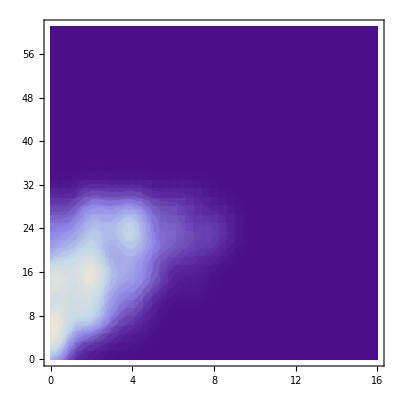
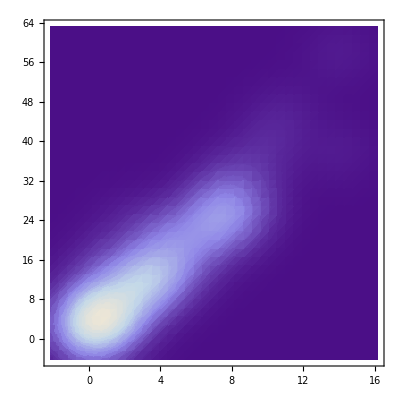
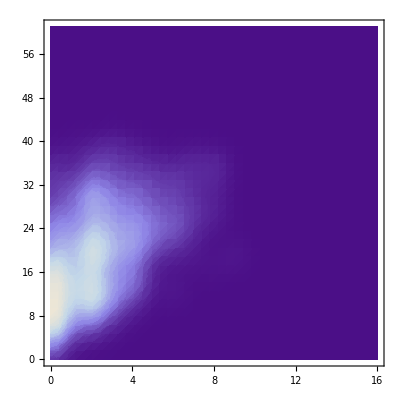

```mathematica
hidepths ={{18,4},{4,1},{5,1},{6,2},{22,7},{4,1},{13,3},{14,4},{5,1},{25,7},{4,1},{22,9},{4,1},{16,4},{3,0},{31,10},{5,2},{14,2},{6,1},{30,14},{2,0},{26,10},{11,4},{2,0},{15,5},{23,8},{21,7},{24,7},{3,1},{21,7},{11,4},{10,3},{7,2},{3,1},{19,7},{5,1},{20,5},{8,1},{5,0},{19,8},{25,8},{17,6},{4,0},{22,7},{2,0},{9,3},{22,9},{9,3},{5,1},{5,1},{9,2},{9,3},{5,0},{8,2},{20,8},{4,1},{14,6},{21,8},{20,7},{18,6},{4,1},{4,0},{9,4},{9,4},{10,3},{10,2},{2,0},{10,2},{15,5},{41,11},{15,5},{13,4},{2,0},{4,0},{5,0},{3,0},{1,0},{2,0},{14,0},{11,3},{6,0},{1,0},{41,14},{1,0},{24,8},{23,9},{10,3},{11,4},{16,4},{17,4}};

hidepthso = {{22,4},{4,1},{5,1},{6,2},{23,7},{4,1},{13,3},{14,4},{5,1},{26,7},{5,1},{27,9},{4,1},{18,4},{3,0},{37,10},{6,2},{23,2},{6,1},{38,14},{2,0},{41,10},{13,4},{3,0},{17,5},{32,8},{27,7},{29,7},{3,1},{24,7},{12,4},{11,3},{7,2},{3,1},{25,7},{5,1},{22,5},{16,1},{6,0},{24,8},{34,8},{20,6},{4,0},{24,7},{2,0},{11,3},{26,9},{12,3},{6,1},{5,1},{12,2},{10,3},{5,0},{8,2},{24,8},{4,1},{16,6},{23,8},{21,7},{19,6},{4,1},{4,0},{11,4},{12,4},{10,3},{12,2},{2,0},{11,2},{15,5},{46,11},{22,5},{14,4},{2,0},{4,0},{5,0},{3,0},{1,0},{2,0},{14,0},{12,3},{6,0},{1,0},{58,14},{1,0},{26,8},{30,9},{11,3},{12,4},{17,4},{21,4}};

{SmoothDensityHistogram[Reverse/@frdepthso,PlotRange->{{0,16},{0,61}}],SmoothDensityHistogram[Reverse/@hidepthso],SmoothDensityHistogram[Reverse/@svdepths,PlotRange->{{0,16},{0,61}}]}
```

```mathematica
#[[2]]/#[[1]]&/@hidepths
```

{2/9,1/4,1/5,1/3,7/22,1/4,3/13,2/7,1/5,7/25,1/4,9/22,1/4,1/4,0,10/31,2/5,1/7,1/6,7/15,0,5/13,4/11,0,1/3,8/23,1/3,7/24,1/3,1/3,4/11,3/10,2/7,1/3,7/19,1/5,1/4,1/8,0,8/19,8/25,6/17,0,7/22,0,1/3,9/22,1/3,1/5,1/5,2/9,1/3,0,1/4,2/5,1/4,3/7,8/21,7/20,1/3,1/4,0,4/9,4/9,3/10,1/5,0,1/5,1/3,11/41,1/3,4/13,0,0,0,0,0,0,0,3/11,0,0,14/41,0,1/3,9/23,3/10,4/11,1/4,4/17}

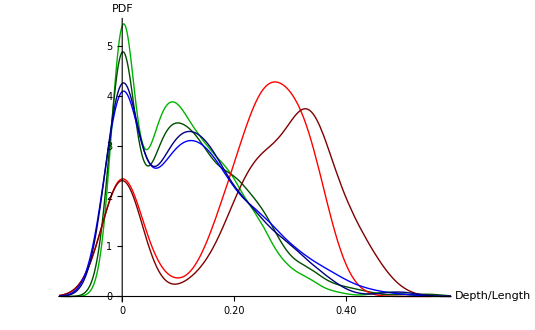

```mathematica
Show[
SmoothHistogram[#[[2]]/#[[1]]&/@svdepthso,PlotStyle->RGBColor[0,0.7,0]],
SmoothHistogram[#[[2]]/#[[1]]&/@svdepths,PlotStyle->RGBColor[0,0.3,0]],

SmoothHistogram[#[[2]]/#[[1]]&/@hidepthso,PlotStyle->Red],SmoothHistogram[#[[2]]/#[[1]]&/@hidepths,PlotStyle->RGBColor[0.5,0,0]],

SmoothHistogram[#[[2]]/#[[1]]&/@frdepthso,PlotStyle->Blue],SmoothHistogram[#[[2]]/#[[1]]&/@depths,PlotStyle->RGBColor[0,0,0.5] ],

AxesLabel->{"Depth/Length","PDF"}
]
```

## Logistic Regression

```mathematica
hifeatures=Import@FileNameJoin[{NotebookDirectory[],"crap_features.csv"}];
frfeatures=Import[FileNameJoin[{NotebookDirectory[],"crap_french_features.csv"}]][[;;100]];
```

```mathematica
H[X_,θ_,hθ_] := Table[Sum[-X[[i,j]]X[[i,k]]hθ[X[[i]], θ](1-hθ[X[[i]], θ]),{i,1,Length[X]}], {j,1,Length[θ]},{k,1,Length[θ]}]
Delθ[X_,Y_,θ_,hθ_]:=Table[Sum[(Y[[i]]-hθ[X[[i]],θ])X[[i,j]],{i,1,Length[X]}],{j,1,Length[θ]}]
Newton[θ_,X_,Y_,hθ_]:= θ- Inverse[H[X,θ,hθ]].Delθ[X,Y,θ,hθ]
Newton[θ_,{X_,Y_,hθ_}]:= Newton[θ,X,Y,hθ]
```

```mathematica
Iterate[func_,n_,initial_,consts_]:=Module[{temp,i},
temp=initial;
For[i=0,i<n,i++,
 temp =func[temp,consts];
];
Return[temp];
];
```

```mathematica
XX=Table[Join[{1.},#[[i]]],{i,1,Length@#}]&@(hifeatures~Join~frfeatures);YY=ConstantArray[{1.}, Length@hifeatures]~Join~ConstantArray[{0.},Length@frfeatures];
```

```mathematica
Clear[sol]
sol[X_,Y_,θ_]:=Iterate[Newton, 100, θ, {X,Y,1/(1+ⅇ^(-#1.Flatten[#2]))&}]
```

```mathematica
sol[XX,YY,{0.,0.,0.}]
```

```mathematica
Show[
BubbleChart[{Flatten/@Tally@hifeatures,Flatten/@Tally@frfeatures}],
Plot[Solve[0.2542553502946426+-0.34731543843304x1+0.33441826042367423x2==0,x2][[1,1,2]],{x1,0,40},PlotStyle->Thick]
]
```

-Graphics-

```mathematica
Length@Select[0.2542553502946426+-0.34731543843304#[[1]]+0.33441826042367423#[[2]]&/@hifeatures,#>=0&]
```

69